Augustine Stav
Professor Onuttom Narayan
May 25, 2016

Phys 242 Homework 7 Part I

1.

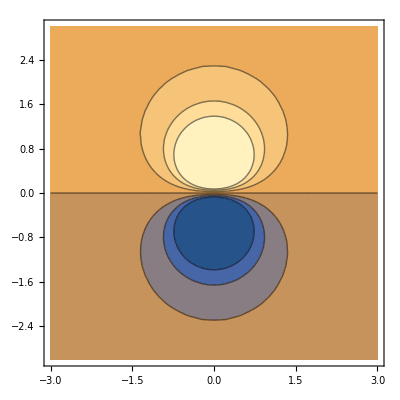

```mathematica
v[x_,z_] := 1/Sqrt[(z-1/2)^2 + x^2] - 1/Sqrt[(z+1/2)^2 + x^2]
ContourPlot[v[x,z], {x, -3, 3}, {z, -3, 3}, ClippingStyle->Automatic]
```

If ClippingStype->Automatic is not used:

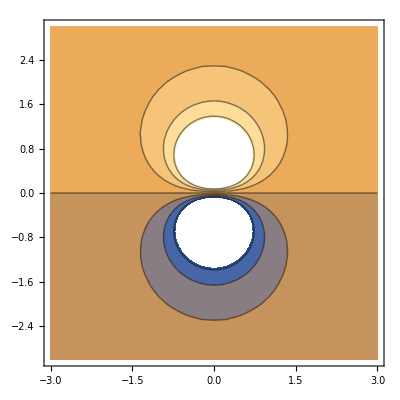

```mathematica
v[x_,z_] := 1/Sqrt[(z-1/2)^2 + x^2] - 1/Sqrt[(z+1/2)^2 + x^2]
ContourPlot[v[x,z], {x, -3, 3}, {z, -3, 3}]
```

The clipped region is whitespace if ClippingStype->Automatic is not used.

2.

{x/((x^2+(-1/2+z)^2)^(3/2))-x/((x^2+(1/2+z)^2)^(3/2)),(-1/2+z)/((x^2+(-1/2+z)^2)^(3/2))-(1/2+z)/((x^2+(1/2+z)^2)^(3/2))}

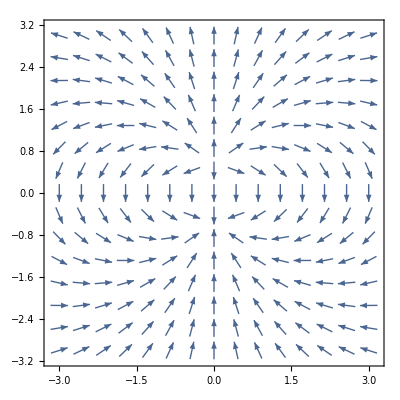

```mathematica
f[x_,z_] = -Grad[v[x,z],{x,z}]
VectorPlot[f[x,z], {x, -3, 3}, {z, -3, 3},VectorScale->{Tiny, Automatic, None}]
```

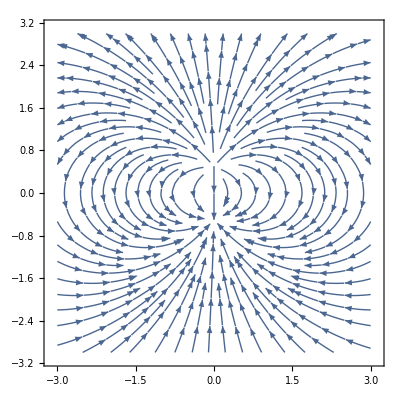

```mathematica
StreamPlot[f[x,z], {x, -3, 3}, {z, -3, 3},VectorScale->{Tiny, Automatic, None}]
```

3.(a) Assuming the root condition is given by ψ2[L] = 0, I was able to find an energy eigenvalue in part (b).

-0.9

37.7325

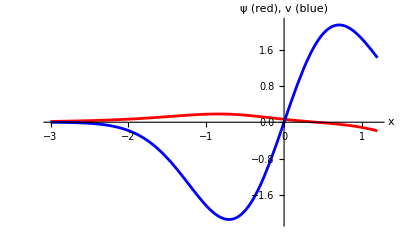

```mathematica
Clear["Global`*"]
L = 5;
v[x_] := 5x Exp[−x^2 ]
ψ1[x_] := Exp[Abs[2 en]^(1/2) x]
eqn[en_] := ψ2''[x] + 2(en - v[x])ψ2[x]
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L] ==  ψ1[-L], ψ2'[-L] ==  ψ1'[-L]},ψ2, {x, -L, L} ])
eval = -0.9
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
ψnn[x_] := efunc2[x] /; -L≤  x
ψnn[x_] := ψ1[x] /; x < -L
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, L} ] ]
ψ[x_] := ψnn[x] / normconst;
fig = Plot[{ψnn[x],v[x]}, {x,-3, 1.2},PlotRange->{-2.2,2.2}, PlotStyle -> {{AbsoluteThickness[2], Red},{AbsoluteThickness[2], Blue}},AxesLabel -> {"x", "ψ (red), v (blue)"} ]
```

```mathematica
_
```

_

3.(b)

Energy:

-0.955984

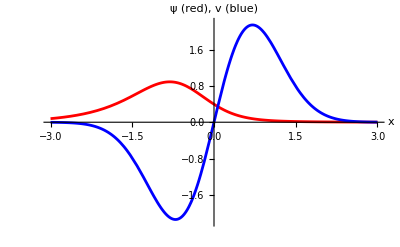

```mathematica
Clear["Global`*"]
L = 5;
v[x_] := 5x Exp[−x^2 ]
ψ1[x_] := Exp[Abs[2 en]^(1/2) x]
eqn[en_] := ψ2''[x] + 2(en - v[x])ψ2[x]
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L] ==  ψ1[-L], ψ2'[-L] ==  ψ1'[-L]},ψ2, {x, -L, L} ])
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
"Energy:"
eval = energy /. FindRoot [ sol2[L, energy],{energy, -0.8, -1} ]
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
ψnn[x_] := 0 /; x > L
ψnn[x_] := efunc2[x] /; -L≤  x ≤ L
ψnn[x_] := ψ1[x] /; x < -L
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
ψ[x_] := ψnn[x] / normconst;
fig = Plot[{ψ[x],v[x]}, {x,-3, 3},PlotRange->{-2.2,2.2}, PlotStyle -> {{AbsoluteThickness[2], Red},{AbsoluteThickness[2], Blue}},AxesLabel -> {"x", "ψ (red), v (blue)"} ]
```

4. Source:

package hw7prob4;
public class Hw7prob4 {
    public static void main(String[] args) {
        int d = 1; //not yet implemented
        int[] p = {0,1,2}; //not yet implemented
        int n = 3;
        
        double[][] a = {{1,2,3},{2,-4,6},{3,-9,-3}};
        double[][] aInverse = new double[n][n];
        System.out.println("Inverse of A:");
        inverse(a, aInverse, n);
        
        double[][] aIterate = new double[n][n];
        double[][] aInverseIterate = new double[n][n];
        System.out.println("2xInverse of A (iterated A):");
        inverse(aInverse, aIterate, n);
        System.out.println("3xInverse of A (iterated inverse of A):");
        inverse(aIterate, aInverseIterate, n);
    }
    public static void inverse(double[][] a, double[][] x, int n){
        double[][] l = new double[n][n];
        double[][] u = new double[n][n];
        
        u[1][0] = u[2][0] = u[2][1] = 0;
        l[0][0] = l[1][1] = l[2][2] = 1;
 
        u[0][0] = a[0][0];
        u[0][1] = a[0][1];
        u[0][2] = a[0][2];
        l[1][0] = a[1][0]/a[0][0];
        l[2][0] = a[2][0]/a[0][0];
        
        u[1][1] = a[1][1] - l[1][0]*u[0][1]; 
        u[1][2] = a[1][2] - l[1][0]*u[0][2];
        l[2][1] = (a[2][1] - l[2][0]*u[0][1])/u[1][1];
        u[2][2] = a[2][2] - l[2][0]*u[0][2] - l[2][1]*u[1][2];
        
        double[][] b = {{1,0,0},{0,1,0},{0,0,1}};
        //double[][] x is the inverse matrix (parameter of the "inverse" method)
        double[][] y = new double[n][n];
        
        for(int i = 0; i < n; i++){
            y[0][i] = b[0][i];
            y[1][i] = b[1][i] - l[1][0]*y[0][i];
            y[2][i] = b[2][i] - l[2][0]*y[0][i] - l[2][1]*y[1][i];

            x[2][i] = y[2][i]/u[2][2];
            x[1][i] = (y[1][i] - u[1][2]*x[2][i])/u[1][1];
            x[0][i] = (y[0][i] - u[0][2]*x[2][i] - u[0][1]*x[1][i])/u[0][0];
        }

        for(int i=0; i<n; i++)
        {
            for(int j=0; j<n; j++)
                System.out.printf("%20.16f",x[i][j]);
            System.out.println();
        }
        System.out.println();
    }
}

Output:

Inverse of A:
  0.6875000000000000 -0.2187500000000000  0.2500000000000000
  0.2500000000000000 -0.1250000000000000 -0.0000000000000000
 -0.0625000000000000  0.1562500000000000 -0.0833333333333333

2xInverse of A (iterated A):
  1.0000000000000002  2.0000000000000004  3.0000000000000000
  2.0000000000000004 -3.9999999999999987  5.9999999999999990
  3.0000000000000000 -9.0000000000000000 -3.0000000000000000

3xInverse of A (iterated inverse of A):
  0.6875000000000000 -0.2187500000000000  0.2500000000000000
  0.2500000000000000 -0.1250000000000000  0.0000000000000000
 -0.0625000000000001  0.1562500000000001 -0.0833333333333334

The iterated A^-1 (the third matrix in the output) does change 
(by 10^-16) due to numerical errors.